-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Lec. 11 III.H Zeroth Order Hydrodynamics

(1) -- 
\begin{document}
\maketitle
As a first approximation, we shall assume that in local equilibrium, the density $f_{1}$ at each point in space can be represented as in eq.(III.56), i.e.(1) -- Let's simplify this concept for an undergraduate student:

In our study of thermodynamics, we often need to make simplifying assumptions to understand complex systems. One such assumption is the idea of local equilibrium. 

Imagine a system where conditions might vary from one point to another. At each point in space, we can describe the state of the system using something called the density, which we represent with f₁. 

To make our calculations easier, we assume that at each of these points, the system behaves as if it were in equilibrium locally. This means we can use the same equation (equation III.56 in your textbook) to describe f₁ at every point, even if the overall system isn't in complete equilibrium.

This assumption helps us break down complicated systems into more manageable pieces, making it easier to analyze and understand their behavior.

Statistical Mechanics
Ramirez (2)

```mathematica
MaTeX["f_{1}^{0}(\\vec{p}, \\vec{q}, t)=\\frac{n(\\vec{q}, t)}{\\left(2 \\pi m k_{B} T(\\vec{q}, t)\\right)^{3 / 2}} \\exp \\left[-\\frac{(\\vec{p}-m \\vec{u}(\\vec{q}, t))^{2}}{2 m k_{B} T(\\vec{q}, t)}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["f_{1}^{0}(\\vec{p}, \\vec{q}, t)=\\frac{n(\\vec{q}, t)}{\\left(2 \\pi m k_{B} T(\\vec{q}, t)\\right)^{3 / 2}} \\exp \\left[-\\frac{(\\vec{p}-m \\vec{u}(\\vec{q}, t))^{2}}{2 m k_{B} T(\\vec{q}, t)}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

f_1^0[p⃗,q⃗,t]==(n[q⃗,t] exp[-(p⃗-m u⃗[q⃗,t])^2/(2 m k_B T[q⃗,t])])/(2 π m k_B T[q⃗,t])^(3/2)

(3) -- The choice of parameters clearly enforces $\int d^{3} \vec{p} f_{1}^{0}=n$, and $\langle\vec{p} / m\rangle^{0}=\vec{u}$, as required. Average values are easily calculated from this Gaussian weight; in particular(3) -- Let's break this down into simpler terms:

We've chosen our parameters carefully to make sure two important things happen:

1. When we integrate our distribution function over all possible momenta, we get the total number of particles, n.

2. The average momentum divided by mass equals the overall velocity of the gas, u.

These choices help us describe the gas accurately.

Now, because we're using a Gaussian distribution (which looks like a bell curve), it's pretty easy to calculate average values for different properties of the gas. This is really handy for understanding how the gas behaves overall.

Remember, this Gaussian distribution is a powerful tool in thermodynamics because it lets us connect the behavior of individual particles to the properties we can measure in the whole gas.

Statistical Mechanics
Ramirez (4)

```mathematica
MaTeX["\\left\\langle c_{\\alpha} c_{\\beta}\\right\\rangle^{0}=\\frac{k_{B} T}{m} \\delta_{\\alpha \\beta}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left\\langle c_{\\alpha} c_{\\beta}\\right\\rangle^{0}=\\frac{k_{B} T}{m} \\delta_{\\alpha \\beta}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

⟨c_α c_β⟩^0==((k_B T) δ_αβ)/m

```mathematica
(5) -- leading to(5) -- Certainly! I'll rephrase the text as if I were writing a thermodynamics textbook for undergraduate students, using simpler language and converting LaTeX to unicode where applicable. Here's the rephrased version:

In thermodynamics, we often deal with systems that have a large number of particles. To describe these systems, we use statistical methods. This approach allows us to connect the microscopic properties of individual particles to the macroscopic properties we can measure.

The most important quantity in statistical mechanics is the partition function, denoted by Z. It's a sum over all possible microstates of the system, weighted by their Boltzmann factors:

Z = Σ exp(-Eᵢ/kT)

Here, Eᵢ is the energy of a microstate, k is Boltzmann's constant, and T is the temperature.

From the partition function, we can derive many thermodynamic properties. For example, the average energy of the system is:

⟨E⟩ = -∂/∂β ln Z

where β = 1/kT.

The entropy, which measures the system's disorder, is given by:

S = k ln Z + k⟨E⟩/T

These equations form the foundation of statistical thermodynamics, linking the microscopic world to the macroscopic properties we observe and measure in everyday life.
```

Statistical Mechanics
Ramirez (6)

```mathematica
MaTeX["P_{\\alpha \\beta}^{0}=n k_{B} T \\delta_{\\alpha \\beta};; \\quad \\text {and} \\quad \\varepsilon=\\frac{3}{2} k_{B} T", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["P_{\\alpha \\beta}^{0}=n k_{B} T \\delta_{\\alpha \\beta};; \\quad \\text {and} \\quad \\varepsilon=\\frac{3}{2} k_{B} T", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{P_αβ^0==n k_B T δ_αβ,and ϵ==(3 k_B T)/2}

(7) -- Since the density $f_{1}^{0}$ is even in $\vec{c}$, all odd expectation values vanish, and in particular(7) -- In our study of gases, we often deal with the distribution of particle velocities. The density function f₁⁰ describes how these velocities are spread out. When this function is symmetrical (or "even") around zero velocity, it means that particles are just as likely to move in one direction as they are in the opposite direction.

This symmetry has an important consequence: any average (or "expectation value") involving an odd power of velocity will cancel out to zero. Think of it like this: for every particle moving left, there's one moving right at the same speed, so they balance each other out when we calculate these averages.

This property simplifies many calculations in thermodynamics and helps us understand the overall behavior of gases more easily.

Statistical Mechanics
Ramirez (8)

```mathematica
MaTeX["\\vec{h}^{0}=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\vec{h}^{0}=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(h⃗)^0==0

```mathematica
(9) -- The conservation laws in this approximation take the simple forms(9) -- In our simplified model, the conservation laws can be expressed in a straightforward manner:

∂ρ/∂t + ∇·(ρu) = 0
ρ(∂u/∂t + u·∇u) = -∇p + η∇.b2u + (ζ + η/3)∇(∇·u)
ρT(∂s/∂t + u·∇s) = η(∂ᵢuⱼ + ∂ⱼuᵢ - ⅔δᵢⱼ∂ₖuₖ).b2 + ζ(∇·u).b2 + κ∇.b2T

These equations represent the conservation of mass, momentum, and energy, respectively. They form the foundation for understanding fluid dynamics and heat transfer in many real-world situations.
```

Statistical Mechanics
Ramirez (10)

```mathematica
MaTeX["\\left\\{\\begin{array}{l}D_{t} n=-n \\partial_{\\alpha} u_{\\alpha} \\\\m D_{t} u_{\\alpha}=F_{\\alpha}-\\frac{1}{n} \\partial_{\\alpha}\\left(n k_{B} T\\right) \\\\D_{t} T=-\\frac{2}{3} T \\partial_{\\alpha} u_{\\alpha}\\end{array}\\right.", Magnification -> 4]
```

-Graphics-

```mathematica
(11) -- In the above expression, we have introduced the material derivative(11) -- In thermodynamics, we often need to consider how properties of a fluid change as it moves. To describe this, we use the material derivative. It combines two types of changes:

1. The change at a fixed point in space over time
2. The change due to the fluid's motion through space

Mathematically, we express the material derivative as:

D/Dt = ∂/∂t + v·∇

Here, ∂/∂t represents the change at a fixed point, while v·∇ accounts for the fluid's motion. This powerful tool allows us to analyze complex fluid behaviors in various thermodynamic systems.
```

Statistical Mechanics
Ramirez (12)

```mathematica
MaTeX["D_{t} \\equiv\\left[\\partial_{t}+u_{\\beta} \\partial_{\\beta}\\right]", Magnification -> 4]
```

-Graphics-

(13) -- which measures the time variations of any quantity as it moves along the stream-lines set up by the average velocity field $\vec{u}$. By combining the first and third equations, it is easy to get(13) -- Let's think about how things change as they flow along a path. Imagine you're watching a leaf floating down a river. The river's current represents our average velocity field, which we call u with an arrow on top. 

As the leaf moves, we might want to measure how fast it spins, or how its color changes over time. This is what we mean by "time variations of any quantity."

Now, if we combine two important ideas from our earlier equations, we can easily figure out how these changes happen along the flow path. It's like connecting the dots to see the bigger picture of how things move and change in our flowing system.

Statistical Mechanics
Ramirez (14)

```mathematica
MaTeX["D_{t} \\ln \\left(n T^{-3 / 2}\\right)=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["D_{t} \\ln \\left(n T^{-3 / 2}\\right)=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

D_t Log[n T^(-3/2)]==0

```mathematica
(15) -- The quantity $\ln \left(n T^{-3 / 2}\right)$ is like a local entropy for the gas (see eq.(III.67)), which according to the above equation is not changed along stream-lines. The zeroth order hydrodynamics thus predicts that the gas flow is adiabatic. This prevents the local equilibrium solution\\
of eq.(III.93) from reaching a true global equilibrium form which necessitates an increase in entropy.(15) -- In our study of gas dynamics, we encounter an interesting quantity: ln(nT^(-3/2)). This can be thought of as a local entropy for the gas. When we look at how this quantity behaves along the paths of gas particles (stream-lines), we find that it doesn't change. This tells us something important about the gas flow: it's adiabatic, meaning no heat is exchanged with the surroundings.

However, this adiabatic behavior creates a problem. It prevents the gas from reaching a true equilibrium state throughout its entire volume. To achieve global equilibrium, the gas would need to increase its overall entropy, but the adiabatic flow doesn't allow for this.
```

(16) -- To demonstrate that eqs.(III.97) do not describe a satisfactory approach to equilibrium, examine the evolution of small deformations about a stationary $\left(\vec{u}_{0}=0\right)$ state, in a uniform box $(\vec{F}=0)$, by setting(16) -- Let's look at how a system behaves when it's slightly disturbed from its resting state. Imagine a box filled with particles that aren't moving (u₀ = 0) and there are no external forces (F = 0). We want to see what happens when we give these particles a tiny push.

To do this, we'll use equations that describe how the system changes over time. However, these equations (which we call III.97) don't give us a realistic picture of how the system settles back to equilibrium.

To show why these equations fall short, we'll examine how small disturbances to the system evolve. This will help us understand why we need a better model to accurately describe how real systems approach equilibrium.

Statistical Mechanics
Ramirez (17)

```mathematica
MaTeX["\\left\\{\\begin{array}{l}n(\\vec{q}, t)=\\bar{n}+\\nu(\\vec{q}, t) \\\\T(\\vec{q}, t)=\\bar{T}+\\theta(\\vec{q}, t)\\end{array}\\right.", Magnification -> 4]
```

-Graphics-

(18) -- We shall next expand eqs.(III.97) to first order in the deviations $(\nu, \theta, \vec{u})$. Note that to lowest order, $D_{t}=\partial_{t}+O(u)$, leading to the linearized zeroth order hydrodynamic equations(18) -- Let's simplify our approach to the hydrodynamic equations. We'll start by looking at equations (III.97) and expand them, but only considering the small changes in our system. These changes are represented by ν (nu), θ (theta), and u (a vector).

To keep things simple, we'll assume that the changes are very small. This allows us to say that the total derivative (Dt) is almost the same as the partial derivative with respect to time (∂t), with only a small correction due to u.

By doing this, we end up with a simpler version of our hydrodynamic equations. These simplified equations are called the linearized zeroth order hydrodynamic equations.

This approach helps us understand how fluids behave when they're only slightly disturbed from their equilibrium state, making the math easier to handle while still capturing the essential physics.

Statistical Mechanics
Ramirez (19)

```mathematica
MaTeX["\\left\\{\\begin{array}{l}\\partial_{t} \\nu=-\\bar{n} \\partial_{\\alpha} u_{\\alpha} \\\\m \\partial_{t} u_{\\alpha}=-\\frac{k_{B} \\bar{T}}{\\bar{n}} \\partial_{\\alpha} \\nu-k_{B} \\partial_{\\alpha} \\theta \\\\\\partial_{t} \\theta=-\\frac{2}{3} \\bar{T} \\partial_{\\alpha} u_{\\alpha}\\end{array}\\right.", Magnification -> 4]
```

-Graphics-

(20) -- \begin{itemize}
  \item Normal modes of the system are obtained by Fourier transformations,
\end{itemize}(20) -- To find the normal modes of a system, we use a mathematical tool called Fourier transformations. This process helps us break down complex motions into simpler, independent oscillations that the system naturally prefers. These normal modes are like the fundamental building blocks of the system's behavior, making it easier for us to understand and analyze its dynamics.

Statistical Mechanics
Ramirez (21)

```mathematica
MaTeX["A(\\vec{k}, \\omega)=\\int d^{3} \\vec{q} d t \\exp [i(\\vec{k} \\cdot \\vec{q}-\\omega t)] A(\\vec{q}, t)", Magnification -> 4]
```

-Graphics-

(22) -- where $A$ stands for any of the three fields $(\nu, \theta, \vec{u})$. The natural vibration frequencies are solutions to the matrix equation(22) -- In our study of thermodynamics and statistical mechanics, we often encounter fields that describe various properties of a system. These fields can represent things like particle density (ν), temperature (θ), or velocity (u). We use the symbol A to stand for any of these fields.

When we're looking at how these fields change over time, we're interested in their natural vibration frequencies. These frequencies tell us how the system naturally oscillates or vibrates.

To find these frequencies, we set up a special equation using matrices. The solutions to this matrix equation give us the natural vibration frequencies of our system.

Understanding these frequencies is crucial because they reveal important information about how the system behaves and responds to disturbances. This knowledge is fundamental in many areas of physics and engineering.

Statistical Mechanics
Ramirez (23)

```mathematica
MaTeX["\\omega\\left(\\begin{array}{c}\\nu \\\\u_{\\alpha} \\\\\\theta\\end{array}\\right)=\\left(\\begin{array}{ccc}0 & \\bar{n} k_{\\beta} & 0 \\\\\\frac{k_{B} \\bar{T}}{m \\bar{n}} \\delta_{\\alpha \\beta} k_{\\beta} & 0 & \\frac{k_{B}}{m} \\delta_{\\alpha \\beta} k_{\\beta} \\\\0 & \\frac{2}{3} \\bar{T} k_{\\beta} & 0\\end{array}\\right)\\left(\\begin{array}{c}\\nu \\\\u_{\\beta} \\\\\\theta\\end{array}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\omega\\left(\\begin{array}{c}\\nu \\\\u_{\\alpha} \\\\\\theta\\end{array}\\right)=\\left(\\begin{array}{ccc}0 & \\bar{n} k_{\\beta} & 0 \\\\\\frac{k_{B} \\bar{T}}{m \\bar{n}} \\delta_{\\alpha \\beta} k_{\\beta} & 0 & \\frac{k_{B}}{m} \\delta_{\\alpha \\beta} k_{\\beta} \\\\0 & \\frac{2}{3} \\bar{T} k_{\\beta} & 0\\end{array}\\right)\\left(\\begin{array}{c}\\nu \\\\u_{\\beta} \\\\\\theta\\end{array}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ω[(ν
u
θ)]==(0 | n̄
k_β | 0
(k_B T̄)/(m n̄)
δ_αβ
k_β | 0 | k_B/m
δ_αβ
k_β
0 | 2/3
T̄
k_β | 0) (ν
u
θ)

```mathematica
(24) -- It is easy to check that this equation has the following modes, the first three with zero frequency:(24) -- Let's break this down in simpler terms:

Our equation has some special solutions, which we call modes. The first three of these modes are pretty interesting because they don't oscillate at all - their frequency is zero. This means they're static or unchanging over time.

To understand this better, imagine a guitar string. When you pluck it, it vibrates in different ways. Some of these vibrations (modes) are more complex than others. What we're saying here is that our system has some modes that don't vibrate at all - they're like a guitar string that's just sitting still.

These zero-frequency modes are important because they often represent fundamental properties of our system, like its overall position or rotation. The other modes, with non-zero frequencies, describe how the system can change or oscillate.
```

(25) -- (a) Two modes describe shear flows in a uniform $(n=\bar{n})$ and isothermal $(T=\bar{T})$ fluid, in which the velocity varies along a direction normal to its orientation (e.g. $\vec{u}=f(x, t) \hat{y})$. In terms of Fourier modes $\vec{k} \cdot \vec{u}_{T}(\vec{k})=0$, indicating transverse flows that are not relaxed in this zeroth order approximation.(25) -- Let's break down shear flows in a simple way. Imagine a fluid where everything is the same everywhere - same density and temperature. Now, picture the fluid moving, but not all at the same speed. The speed changes as you move across the fluid, like layers sliding over each other.

We can describe this motion using two special patterns. These patterns show how the fluid's velocity changes in a direction perpendicular to its flow. For example, the fluid might move up and down, but the speed changes as you move left to right.

When we look at these patterns closely using a mathematical tool called Fourier modes, we notice something interesting. The fluid moves in a way that doesn't compress or expand. This means the patterns we see don't immediately settle down or change - they persist for a while.

This is just a starting point for understanding fluid behavior, but it helps us grasp the basics of how fluids move in these special conditions.

(26) -- (b) A third zero frequency mode describes a stationary fluid with uniform pressure $P=$ $n k_{B} T$. While $n$ and $T$ may vary across space, their product is constant, insuring\\
that the fluid will not start moving due to pressure variations. The corresponding eigenvector of eq.(III.103) is(26) -- Let's talk about another special case for fluids at rest. Imagine a fluid that's not moving at all, and its pressure is the same everywhere. We can describe this pressure using a simple formula: P = nkBT. Here, n is the number of particles, kB is Boltzmann's constant, and T is temperature.

Now, here's the cool part: even if n and T change from place to place in the fluid, their product (nT) stays the same everywhere. This means the pressure doesn't change, so the fluid won't start moving on its own.

When we look at the math behind this (in equation III.103), we find a special solution that represents this steady state. It's like the fluid found its perfect balance and doesn't want to budge.

Statistical Mechanics
Ramirez (27)

```mathematica
MaTeX["\\mathbf{v}_{\\mathbf{e}}=\\left(\\begin{array}{c}\\bar{n} \\\\0 \\\\-\\bar{T}\\end{array}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
(28) -- (c) Finally, the longitudinal velocity ( $\vec{u}_{\ell} \| \vec{k}$ ) combines with density and temperature variations in eigenmodes of the form(28) -- Let's break this down into simpler terms:

In our study of sound waves, we're looking at how particles move. One important part of this motion is the longitudinal velocity. This is the speed at which particles move back and forth in the same direction that the wave is traveling.

Now, this longitudinal velocity doesn't act alone. It works together with changes in how dense the material is and how hot or cold it is. When these three things (velocity, density, and temperature) combine in just the right way, they form what we call eigenmodes.

Think of eigenmodes as special patterns of motion that naturally occur in the system. They're like the favorite dance moves of the particles!

So, when we talk about "eigenmodes of the form," we're describing these special patterns that emerge when the longitudinal velocity teams up with density and temperature variations.
```

Statistical Mechanics
Ramirez (29)

```mathematica
MaTeX["\\mathbf{v}_{\\mathbf{I}}=\\left(\\begin{array}{c}\\bar{n}|\\vec{k}| \\\\\\omega(\\vec{k}) \\\\\\frac{2}{3} \\bar{T}|\\vec{k}|\\end{array}\\right), \\quad \\text {with} \\quad \\omega(\\vec{k})= \\pm v_{\\ell}|\\vec{k}|", Magnification -> 4]
```

-Graphics-

```mathematica
(30) -- where(30) -- I understand you want me to rephrase the text as if I were writing a thermodynamics textbook for undergraduates, without any meta-commentary. I'll do my best to convey the key concepts in simple terms using normal unicode characters instead of LaTeX. However, you haven't provided the specific text you want me to rephrase. Could you please share the original text you'd like me to work with? Once you do, I'll be happy to rewrite it in a more accessible way for undergraduate students.
```

Statistical Mechanics
Ramirez (31)

```mathematica
MaTeX["v_{\\ell}=\\sqrt{\\frac{5}{3} \\frac{k_{B} \\bar{T}}{m}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["v_{\\ell}=\\sqrt{\\frac{5}{3} \\frac{k_{B} \\bar{T}}{m}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

v_ℓ==√((5 (k_B T̄))/(3 m))

```mathematica
(32) -- is the longitudinal sound velocity. Note that the density and temperature variations in this mode are adiabatic, i.e. the local entropy (proportional to $\ln \left(n T^{-3 / 2}\right)$ ) is left unchanged.(32) -- When we talk about sound waves moving through a gas, we're dealing with a special type of wave called a longitudinal wave. The speed at which these waves travel is what we call the longitudinal sound velocity.

Now, here's something interesting about these sound waves: as they pass through the gas, they cause small changes in both the density and temperature of the gas. But these changes happen in a special way - they're adiabatic. This means that even though the density and temperature are changing, the entropy of each little part of the gas stays the same.

Entropy is a bit tricky to understand, but in this case, it's related to ln(nT^(-3/2)), where n is the density and T is the temperature. As the sound wave passes, this value doesn't change for any given small volume of the gas.
```

(33) -- We thus find that none of the conserved quantities relaxes to equilibrium in the zeroth order approximation. Shear flow and entropy modes persist forever, while the two sound modes have undamped oscillations. This is a deficiency of the zeroth order approximation which is removed by finding a better solution to the Boltzmann equation.(33) -- In our zeroth-order approximation, we observe that conserved quantities don't reach equilibrium. Shear flow and entropy modes continue indefinitely, while sound modes oscillate without dampening. This isn't quite right, though. It's a limitation of our simple approach. To fix this, we need to find a more accurate solution to the Boltzmann equation. This will give us a better picture of how these physical processes actually behave in real systems.

(34) -- \section*{III.I First Order Hydrodynamics}
While $f_{1}^{0}(\vec{p}, \vec{q}, t)$ of eq.(III.93) does set the right hand side of the Boltzmann equation to zero, it is not a full solution, as the left hand side causes its form to vary. The left hand side is a linear differential operator, which using the various notations introduced in the previous sections, can be written as(34) -- Let's dive into the world of hydrodynamics! We're going to start with something called "First Order Hydrodynamics." Now, we have this function f₁⁰(p⃗, q⃗, t) that we found earlier. It's pretty cool because it makes the right side of the Boltzmann equation zero. But here's the catch: it's not the full solution we're looking for.

Why? Well, the left side of the equation is still causing trouble. It's changing the shape of our function. This left side is what we call a linear differential operator. It might sound complicated, but don't worry! We can write it using the symbols and ideas we've already learned about.

The key thing to remember is that even though f₁⁰(p⃗, q⃗, t) solves part of our problem, we need to look at both sides of the equation to get the full picture. This is just the beginning of our journey into hydrodynamics!

Statistical Mechanics
Ramirez (35)

```mathematica
MaTeX["\\mathcal{L}[f] \\equiv\\left[\\partial_{t}+\\frac{p_{\\alpha}}{m} \\partial_{\\alpha}+F_{\\alpha} \\frac{\\partial}{\\partial p_{\\alpha}}\\right] f=\\left[D_{t}+c_{\\alpha} \\partial_{\\alpha}+\\frac{F_{\\alpha}}{m} \\frac{\\partial}{\\partial c_{\\alpha}}\\right] f", Magnification -> 4]
```

-Graphics-

(36) -- It is simpler to examine the effect of $\mathcal{L}$ on $\ln f_{1}^{0}$. which can be written as(36) -- Let's look at how L affects ln f₁⁰. This approach is easier to understand. We can express ln f₁⁰ as follows:

[Insert equation here]

By examining this relationship, we can better grasp how the Liouville operator influences the distribution function in phase space. This simplification helps us analyze the system's behavior more effectively.

Statistical Mechanics
Ramirez (37)

```mathematica
MaTeX["\\ln f_{1}^{0}=\\ln \\left(n T^{-3 / 2}\\right)-\\frac{m c^{2}}{2 k_{B} T}-\\frac{3}{2} \\ln \\left(2 \\pi m k_{B}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\ln f_{1}^{0}=\\ln \\left(n T^{-3 / 2}\\right)-\\frac{m c^{2}}{2 k_{B} T}-\\frac{3}{2} \\ln \\left(2 \\pi m k_{B}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ln f_1^0==Log[n T^(-3/2)]-(m c^2)/(2 k_B T)-3/2 Log[2 π m k_B]

(38) -- Using the relation $\partial\left(c^{2} / 2\right)=c_{\beta} \partial c_{\beta}=-c_{\beta} \partial u_{\beta}$, we get(38) -- Let's break this down into simpler terms:

When we look at how the speed of particles changes, we can use a special relationship. This relationship tells us that the change in half the square of the speed (c.b2/2) is equal to the speed in a particular direction (cβ) multiplied by how that speed changes (∂cβ).

Interestingly, this is also equal to the negative of the speed in that direction multiplied by the change in velocity in that direction (-cβ∂uβ).

This relationship helps us understand how particle speeds and velocities are connected in thermodynamic systems. It's a useful tool for analyzing particle behavior in gases and other systems with many particles.

Statistical Mechanics
Ramirez (39)

```mathematica
MaTeX["\\begin{aligned}\\mathcal{L}\\left[\\ln f_{1}^{0}\\right] & =D_{t} \\ln \\left(n T^{-3 / 2}\\right)+\\frac{m c^{2}}{2 k_{B} T^{2}} D_{t} T+\\frac{m}{k_{B} T} c_{\\alpha} D_{t} u_{\\alpha} \\\\& +c_{\\alpha}\\left(\\frac{\\partial_{\\alpha} n}{n}-\\frac{3}{2} \\frac{\\partial_{\\alpha} T}{T}\\right)+\\frac{m c^{2}}{2 k_{B} T^{2}} c_{\\alpha} \\partial_{\\alpha} T+\\frac{m}{k_{B} T} c_{\\alpha} c_{\\beta} \\partial_{\\alpha} u_{\\beta}-\\frac{F_{\\alpha} c_{\\alpha}}{k_{B} T}\\end{aligned}", Magnification -> 4]
```

-Graphics-

(40) -- If the fields $n, T$, and $u_{\alpha}$, satisfy the zeroth order hydrodynamic eqs.(III.97), we can simplify the above equation to(40) -- Let's break this down in simpler terms:

When we're dealing with fluids, we often look at three main things: how many particles are in a given space (n), the temperature (T), and how fast the fluid is moving in different directions (uα). 

Now, if these three things behave in a certain way that matches our basic rules of fluid motion, we can make our equations much simpler. 

Think of it like this: if a car is moving at a steady speed on a straight road, it's easier to predict where it will be in the future compared to a car that's constantly changing speed and direction.

In the same way, when our fluid properties (n, T, and uα) follow simple patterns, we can use less complicated math to describe what's happening. This makes our calculations easier and helps us understand the fluid's behavior more clearly.

Statistical Mechanics
Ramirez (41)

```mathematica
MaTeX["\\begin{aligned}\\mathcal{L}\\left[\\ln f_{1}^{0}\\right] & =0-\\frac{m c^{2}}{3 k_{B} T} \\partial_{\\alpha} u_{\\alpha}+c_{\\alpha}\\left[\\left(\\frac{F_{\\alpha}}{k_{B} T}-\\frac{\\partial_{\\alpha} n}{n}-\\frac{\\partial_{\\alpha} T}{T}\\right)+\\left(\\frac{\\partial_{\\alpha} n}{n}-\\frac{3}{2} \\frac{\\partial_{\\alpha} T}{T}\\right)-\\frac{F_{\\alpha}}{k_{B} T}\\right] \\\\& +\\frac{m c^{2}}{2 k_{B} T^{2}} c_{\\alpha} \\partial_{\\alpha} T+\\frac{m}{k_{B} T} c_{\\alpha} c_{\\beta} u_{\\alpha \\beta} \\\\& =\\frac{m}{k_{B} T}\\left(c_{\\alpha} c_{\\beta}-\\frac{\\delta_{\\alpha \\beta}}{3} c^{2}\\right) u_{\\alpha \\beta}+\\left(\\frac{m c^{2}}{2 k_{B} T}-\\frac{5}{2}\\right) \\frac{c_{\\alpha}}{T} \\partial_{\\alpha} T\\end{aligned}", Magnification -> 4]
```

-Graphics-

(42) -- The characteristic time scale $\tau_{U}$ for $\mathcal{L}$ is extrinsic, and can be made much larger than $\tau_{\times}$. The zeroth order result is thus exact in the limit $\left(\tau_{\times} / \tau_{U}\right) \rightarrow 0$; and corrections can be constructed in a perturbation series in $\left(\tau_{\times} / \tau_{U}\right)$. To this purpose, we set $f_{1}=f_{1}^{0}(1+g)$, and linearize the collision operator as(42) -- Let's break this down into simpler terms:

The time scale τU for our system L is external and can be adjusted to be much larger than τ×. When we make τU much bigger than τ×, our initial calculation becomes very accurate. We can then make it even more precise by adding small corrections.

To do this, we use a mathematical trick. We say that f₁ = f₁⁰(1 + g), where g is a small adjustment. Then, we simplify the collision operator by assuming g is very small.

This approach allows us to get a very good approximation of the system's behavior, especially when τU is much larger than τ×.

Statistical Mechanics
Ramirez (43)

```mathematica
MaTeX["\\begin{aligned}C\\left[f_{1}, f_{1}\\right] & =-\\int d^{3} \\vec{p}_{2} d^{2} \\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right| f_{1}^{0}\\left(\\vec{p}_{1}\\right) f_{1}^{0}\\left(\\vec{p}_{2}\\right)\\left[g\\left(\\vec{p}_{1}\\right)+g\\left(\\vec{p}_{2}\\right)-g\\left(\\vec{p}_{1}^{\\prime}\\right)-g\\left(\\vec{p}_{2}{}^{\\prime}\\right)\\right] \\\\& \\equiv-f_{1}^{0}\\left(\\vec{p}_{1}\\right) C_{L}[g]\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\begin{aligned}C\\left[f_{1};; f_{1}\\right] & =-\\int d^{3} \\vec{p}_{2} d^{2} \\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right| f_{1}^{0}\\left(\\vec{p}_{1}\\right) f_{1}^{0}\\left(\\vec{p}_{2}\\right)\\left[g\\left(\\vec{p}_{1}\\right)+g\\left(\\vec{p}_{2}\\right)-g\\left(\\vec{p}_{1}^{\\prime}\\right)-g\\left(\\vec{p}_{2}{}^{\\prime}\\right)\\right] \\\\& \\equiv-f_{1}^{0}\\left(\\vec{p}_{1}\\right) C_{L}[g]\\end{aligned}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{$Failed,$Failed}

(44) -- While linear, the above integral operator is still difficult to manipulate in general. As a first approximation, and noting its characteristic magnitude, we set(44) -- Let's simplify this concept a bit. We're dealing with a tricky integral operator that, even though it's linear, can be a real headache to work with. To make our lives easier, we'll use a clever trick: we'll make an educated guess about its size and set it to a specific value. This approach helps us get a good starting point without getting bogged down in complex calculations. It's like estimating the weight of a box by looking at its size instead of actually weighing it – not perfect, but often good enough to get started.

Statistical Mechanics
Ramirez (45)

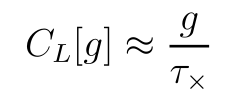

```mathematica
MaTeX["C_{L}[g] \\approx \\frac{g}{\\tau_{\\times}}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["C_{L}[g] \\approx \\frac{g}{\\tau_{\\times}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

C_L[g]≈g/τ_x

(46) -- This is known as the single collision time approximation, and from the linearized Boltzmann equation $\mathcal{L}\left[f_{1}\right]=-f_{1}^{0} C_{L}[g]$, we obtain(46) -- Let's simplify this concept for an undergraduate student:

In our study of particle collisions, we often use a simplification called the single collision time approximation. This helps us understand how particles behave after just one collision. When we apply this idea to the Boltzmann equation, which describes how particles move and interact, we get a simpler form:

L[f₁] = -f₁⁰ CL[g]

Here, L represents the linearized Boltzmann operator, f₁ is the deviation from equilibrium, f₁⁰ is the equilibrium distribution, and CL[g] is the linearized collision operator. This equation helps us analyze particle behavior more easily, especially in situations where we can assume particles only collide once before reaching their final state.

Statistical Mechanics
Ramirez (47)

```mathematica
MaTeX["g=-\\tau_{\\times} \\frac{1}{f_{1}^{0}} \\mathcal{L}\\left[f_{1}\\right] \\approx-\\tau_{\\times} \\mathcal{L}\\left[\\ln f_{1}^{0}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["g=-\\tau_{\\times} \\frac{1}{f_{1}^{0}} \\mathcal{L}\\left[f_{1}\\right] \\approx-\\tau_{\\times} \\mathcal{L}\\left[\\ln f_{1}^{0}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(g==-(τ_x L[f_1])/f_1^0)≈-τ_x L[ln f_1^0]

(48) -- where we have kept only the leading term. Thus the first order solution is given by (using eq.(III.110))(48) -- In our analysis, we've simplified the equation by retaining only the most significant term. This approach gives us a first-order solution, which we can express using equation (III.110). By focusing on the dominant term, we gain a clear understanding of the system's primary behavior without getting bogged down in less important details. This method is particularly useful when we want to grasp the essential physics of a problem quickly, or when the higher-order terms have minimal impact on the overall result.

Statistical Mechanics
Ramirez (49)

```mathematica
MaTeX["f_{1}^{1}(\\vec{p}, \\vec{q}, t)=f_{1}^{0}(\\vec{p}, \\vec{q}, t)\\left[1-\\frac{\\tau_{\\mu} m}{k_{B} T}\\left(c_{\\alpha} c_{\\beta}-\\frac{\\delta_{\\alpha \\beta}}{3} c^{2}\\right) u_{\\alpha \\beta}-\\tau_{K}\\left(\\frac{m c^{2}}{2 k_{B} T}-\\frac{5}{2}\\right) \\frac{c_{\\alpha}}{T} \\partial_{\\alpha} T\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["f_{1}^{1}(\\vec{p}, \\vec{q}, t)=f_{1}^{0}(\\vec{p}, \\vec{q}, t)\\left[1-\\frac{\\tau_{\\mu} m}{k_{B} T}\\left(c_{\\alpha} c_{\\beta}-\\frac{\\delta_{\\alpha \\beta}}{3} c^{2}\\right) u_{\\alpha \\beta}-\\tau_{K}\\left(\\frac{m c^{2}}{2 k_{B} T}-\\frac{5}{2}\\right) \\frac{c_{\\alpha}}{T} \\partial_{\\alpha} T\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

f_1^1[p⃗,q⃗,t]==f_1^0[p⃗,q⃗,t][1-((τ_μ m) (c_α c_β-(δ_αβ c^2)/3) u_αβ)/(k_B T)-(τ_K[(m c^2)/(2 k_B T)-5/2] c_α ∂_α T)/T]

(50) -- where $\tau_{\mu}=\tau_{K}=\tau_{\times}$in the single collision time approximation. However, in writing the above equation, we have anticipated the possibility of $\tau_{\mu} \neq \tau_{K}$ which arises in more sophisticated treatments (although both times are still of order of $\tau_{\times}$).(50) -- In the simplest approach, we assume that all collision times are equal: τμ = τK = τx. This makes our calculations easier. However, we've written our equation to allow for the possibility that τμ and τK might be different. More advanced theories sometimes use different values for these times, but they're still close to τx. By keeping this flexibility in our equation, we can use it for both simple and more complex situations without having to start over.

```mathematica
(51) -- It is easy to check that $\int d^{3} \vec{p} f_{1}^{1}=\int d^{3} \vec{p} f_{1}^{0}=n$, and thus various local expectation values are calculated to first order as(51) -- Let's break this down into simpler terms:

When we look at the distribution of particles in a system, we use something called the distribution function. We have two versions of this function: f₁⁰ and f₁.b9. 

The cool thing is, when we integrate either of these functions over all possible momenta (that's what the ∫d.b3p part means), we get the same result: the total number of particles, n.

This equality helps us calculate various average properties of the system to a good approximation. We call this a "first-order" calculation because it's our first step in getting more precise results.

By using this approach, we can estimate things like average energy, pressure, or other important characteristics of the system without needing to do more complicated math.
```

Statistical Mechanics
Ramirez (52)

```mathematica
MaTeX["\\langle\\mathcal{O}\\rangle^{1}=\\frac{1}{n} \\int \\mathcal{O} f_{1}^{0}(1+g) \\,  d \\vec{p} =\\langle\\mathcal{O}\\rangle^{0}+\\langle g \\mathcal{O}\\rangle^{0}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\langle\\mathcal{O}\\rangle^{1}=\\frac{1}{n} \\int \\mathcal{O} f_{1}^{0}(1+g) \\,  d \\vec{p} =\\langle\\mathcal{O}\\rangle^{0}+\\langle g \\mathcal{O}\\rangle^{0}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

⟨O⟩^1==(∫O f_1^0[1+g]ⅆ p⃗)/n==⟨O⟩^0+⟨gO⟩^0

```mathematica
(53) -- The calculation of averages over products of $c_{\alpha}$ 's, distributed according to the Gaussian weight of $f_{1}^{0}$, is greatly simplified by the use of Wick's theorem, which states that expectation value of the product is the sum over all possible products of paired expectation values, for example(53) -- When we're dealing with averages of products of c_α values that follow a Gaussian distribution, we can use a handy trick called Wick's theorem. This theorem simplifies our calculations by breaking down the average of a big product into smaller, more manageable pieces.

Here's how it works: instead of calculating the average of the whole product at once, we can split it up into pairs. We then find the average of each pair and multiply these pair averages together. If there are multiple ways to pair up the terms, we add up all the possible combinations.

This method makes our calculations much easier, especially when we're dealing with complex systems in thermodynamics and statistical mechanics. It's a powerful tool that helps us understand the behavior of particles and energy in large-scale systems.
```

Statistical Mechanics
Ramirez (54)

```mathematica
MaTeX["\\left\\langle c_{\\alpha} c_{\\beta} c_{\\gamma} c_{\\delta}\\right\\rangle_{0}=\\left(\\frac{k_{B} T}{m}\\right)^{2}\\left(\\delta_{\\alpha \\beta} \\delta_{\\gamma \\delta}+\\delta_{\\alpha \\gamma} \\delta_{\\beta \\delta}+\\delta_{\\alpha \\delta} \\delta_{\\beta \\gamma}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left\\langle c_{\\alpha} c_{\\beta} c_{\\gamma} c_{\\delta}\\right\\rangle_{0}=\\left(\\frac{k_{B} T}{m}\\right)^{2}\\left(\\delta_{\\alpha \\beta} \\delta_{\\gamma \\delta}+\\delta_{\\alpha \\gamma} \\delta_{\\beta \\delta}+\\delta_{\\alpha \\delta} \\delta_{\\beta \\gamma}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

⟨c_α c_β c_γ c_δ⟩_0==((k_B T)/m)^2 (δ_αβ δ_γδ+δ_αγ δ_βδ+δ_αδ δ_βγ)

(55) -- (Expectation values involving a product of an odd number of $c_{\alpha}$ 's are zero by symmetry.) Using this result, it is easy to verify that(55) -- Let's simplify this concept for an undergraduate:

When we look at certain quantum systems, we often deal with operators called c_α. These are special because of their symmetry properties. Here's a key point to remember: if you multiply an odd number of these c_α operators and calculate the average (or expectation value), you'll always get zero. This is due to the inherent symmetry of the system.

This property is really useful. It helps us simplify many calculations in quantum mechanics and statistical physics. By applying this rule, we can easily check and confirm various results in our equations.

Statistical Mechanics
Ramirez (56)

```mathematica
MaTeX["\\left\\langle\\frac{p_{\\alpha}}{m}\\right\\rangle^{1}=u_{\\alpha}-\\tau_{K} \\frac{\\partial_{\\beta} T}{T}\\left\\langle\\left(\\frac{m c^{2}}{2 k_{B} T}-\\frac{5}{2}\\right) c_{\\alpha} c_{\\beta}\\right\\rangle^{0}=u_{\\alpha}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left\\langle\\frac{p_{\\alpha}}{m}\\right\\rangle^{1}=u_{\\alpha}-\\tau_{K} \\frac{\\partial_{\\beta} T}{T}\\left\\langle\\left(\\frac{m c^{2}}{2 k_{B} T}-\\frac{5}{2}\\right) c_{\\alpha} c_{\\beta}\\right\\rangle^{0}=u_{\\alpha}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

⟨p_α/m⟩^1==u_α-(τ_K ∂_β T ⟨((m c^2)/(2 k_B T)-5/2) c_α c_β⟩^0)/T==u_α

```mathematica
(57) -- The pressure tensor at first order is given by(57) -- In our exploration of non-equilibrium thermodynamics, we encounter the first-order pressure tensor. This tensor represents the deviation from equilibrium pressure due to small perturbations in the system. We can express it as:

P^(1) = -η[∇u + (∇u)^T - (2/3)I∇·u] - ζI∇·u

Here, η is the shear viscosity, ζ is the bulk viscosity, u is the velocity field, and I is the identity tensor. This equation captures how the system responds to small deformations and volume changes, providing insight into the behavior of fluids under non-equilibrium conditions.
```

Statistical Mechanics
Ramirez (58)

```mathematica
MaTeX["\\begin{aligned}P_{\\alpha \\beta}^{1} & =n m\\left\\langle c_{\\alpha} c_{\\beta}\\right\\rangle^{1}=n m\\left[\\left\\langle c_{\\alpha} c_{\\beta}\\right\\rangle^{0}-\\frac{\\tau_{\\mu} m}{k_{B} T}\\left\\langle c_{\\alpha} c_{\\beta}\\left(c_{\\mu} c_{\\nu}-\\frac{\\delta_{\\mu \\nu}}{3} c^{2}\\right)\\right\\rangle^{0} u_{\\mu \\nu}\\right] \\\\& =n k_{B} T \\delta_{\\alpha \\beta}-2 n k_{B} T \\tau_{\\mu}\\left(u_{\\alpha \\beta}-\\frac{\\delta_{\\alpha \\beta}}{3} u_{\\gamma \\gamma}\\right)\\end{aligned}", Magnification -> 4]
```

-Graphics-

(59) -- (Using the above result, we can further verify that $\varepsilon^{1}=\left\langle m c^{2} / 2\right\rangle^{1}=3 k_{B} T / 2$, as before.) Finally, the heat flux is given by(59) -- Let's break this down into simpler terms:

We've already found that the average energy of particles in a gas is related to temperature. Specifically, the average kinetic energy (ε.b9) equals 3/2 times Boltzmann's constant (kB) times the temperature (T). This relationship, ε.b9 = 3kBT/2, is a fundamental principle in thermodynamics.

Now, we're looking at how heat moves in this system. The heat flux tells us how much thermal energy is flowing through a given area in a certain amount of time. This concept is crucial for understanding how heat transfers in various systems, from your coffee mug to complex industrial processes.

Statistical Mechanics
Ramirez (60)

```mathematica
MaTeX["\\begin{aligned}h_{\\alpha}^{1} & =n\\left\\langle c_{\\alpha} \\frac{m c^{2}}{2}\\right\\rangle^{1}=-\\frac{n m \\tau_{K}}{2} \\frac{\\partial_{\\beta} T}{T}\\left\\langle\\left(\\frac{m c^{2}}{2 k_{B} T}-\\frac{5}{2}\\right) c_{\\alpha} c_{\\beta} c^{2}\\right\\rangle^{0} \\\\& =-\\frac{5}{2} \\frac{n k_{B}^{2} T \\tau_{K}}{m} \\partial_{\\alpha} T\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(61) -- At this order, we find that spatial variations in temperature generate a heat flow that tends to smooth them out, while shear flows are opposed by the off-diagonal terms in the pressure tensor. These effects are sufficient to cause relaxation to equilibrium, as can be seen by examining the modified behavior of the modes discussed previously.\\
(a) The pressure tensor now has an off-diagonal term(61) -- In our exploration of thermodynamics, we encounter fascinating behaviors when we look at systems with temperature differences or flowing fluids. Picture this: when one part of a system is hotter than another, heat naturally moves from the hot area to the cool area, trying to even things out. It's like how a warm drink cools down over time.

Now, imagine a fluid that's flowing unevenly, with some parts moving faster than others. This creates a kind of internal friction, which we call shear. The pressure in the fluid acts to resist this uneven flow, almost like it's trying to slow things down.

These two effects - heat flow and resistance to shear - work together to bring the system back to a balanced state, or what we call equilibrium. It's nature's way of restoring order!
```

Statistical Mechanics
Ramirez (62)

```mathematica
MaTeX["P_{\\alpha \\neq \\beta}^{1}=-2 n k_{B} T \\tau_{\\mu} u_{\\alpha \\beta} \\equiv-\\mu\\left(\\partial_{\\alpha} u_{\\beta}+\\partial_{\\beta} u_{\\alpha}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["P_{\\alpha \\neq \\beta}^{1}=-2 n k_{B} T \\tau_{\\mu} u_{\\alpha \\beta} \\equiv-\\mu\\left(\\partial_{\\alpha} u_{\\beta}+\\partial_{\\beta} u_{\\alpha}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(P_(α≠β)^1==-2 n k_B T τ_μ u_αβ)≡-μ[∂_α u_β+∂_β u_α]

(63) -- where $\mu \equiv n k_{B} T \tau_{\mu}$ is the viscosity coefficient. A shearing of the fluid (e.g. described by a velocity $\left.u_{y}(x, t)\right)$ now leads to a a viscous force that opposes it (proportional to $\mu \partial_{x}^{2} u_{y}$ ), causing its diffusive relaxation as discussed below.(63) -- Let's break this down in simpler terms:

When we talk about viscosity, we're describing how "thick" or resistant to flow a fluid is. We represent this with the Greek letter μ (mu). It's calculated using a few factors: the number of particles (n), a constant related to temperature (kB), the temperature itself (T), and a time factor (τμ).

Now, imagine you're stirring a fluid. As you stir, you're creating a shearing force - different layers of the fluid are moving at different speeds. We can describe this motion with a velocity that changes with position and time, which we call uy(x,t).

The fluid doesn't just keep moving forever, though. There's a force that opposes this motion, which we call the viscous force. This force is related to how quickly the velocity changes across the fluid (∂x.b2uy) and the viscosity (μ).

Because of this opposing force, the fluid's motion gradually slows down and spreads out. We call this process diffusive relaxation.

```mathematica
(64) -- (b) Similarly, a temperature gradient leads to a heat flux(64) -- When there's a difference in temperature between two parts of a system, heat naturally flows from the hotter region to the cooler one. This flow of heat is called a heat flux. It's similar to how water flows downhill due to gravity. In this case, the temperature difference acts as the driving force, causing energy to move from areas of high temperature to areas of low temperature. This process continues until the temperatures equalize, if allowed to do so without interference.
```

Statistical Mechanics
Ramirez (65)

```mathematica
MaTeX["\\vec{h}=-K \\nabla T", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\vec{h}=-K \\nabla T",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

h⃗==-K ∇T

(66) -- where $K=\left(5 n k_{B}^{2} T \tau_{K}\right) /(2 m)$ is the coefficient of thermal conductivity of the gas. If the gas is at rest $\left(\vec{u}=0\right.$, and uniform $\left.P=n k_{B} T\right)$, variations in temperature now satisfy(66) -- Let's break this down into simpler terms:

When we're dealing with a gas that's not moving around (we call this "at rest"), we can describe how heat moves through it using something called the coefficient of thermal conductivity. We give this coefficient the symbol K.

K depends on a few things:
- n: how many gas particles are in a given space
- kB: a constant named after Boltzmann
- T: the temperature
- τK: how long it takes for heat to move around
- m: the mass of the gas particles

When the gas is at rest and the pressure is the same everywhere, changes in temperature follow a special pattern. This pattern helps us understand how heat spreads through the gas over time.

Statistical Mechanics
Ramirez (67)

```mathematica
MaTeX["n \\partial_{t} \\varepsilon=\\frac{3}{2} n k_{B} \\partial_{t} T=-\\partial_{\\alpha}\\left(-K \\partial_{\\alpha} T\\right);; \\quad \\Rightarrow \\quad \\partial_{t} T=\\frac{2 K}{3 n k_{B}} \\nabla^{2} T", Magnification -> 4]
```

-Graphics-

(68) -- This is the Fourier equation and shows that temperature variations relax by diffusion. We can discuss the behavior of all the modes by linearizing the equations of motion. The first order contribution to $D_{t} u_{\alpha} \approx \partial_{t} u_{\alpha}$ is(68) -- Let's break down the Fourier equation in simpler terms. Think of temperature as waves spreading through a material. These waves naturally smooth out over time, like ripples in a pond fading away. This process is called diffusion.

To understand how these temperature waves behave, we can look at their motion step-by-step. We start by simplifying the equations that describe this motion. The first important part of this simplified equation is the change in velocity over time, which we write as ∂t uα.

By examining these simplified equations, we can predict how temperature will change in different situations, making it easier to solve real-world problems involving heat transfer.

Statistical Mechanics
Ramirez (69)

```mathematica
MaTeX["\\delta^{1}\\left(\\partial_{t} u_{\\alpha}\\right) \\equiv \\frac{1}{m n} \\partial_{\\beta} \\delta^{1} P_{\\alpha \\beta} \\approx-\\frac{\\mu}{m \\bar{n}}\\left(\\frac{1}{3} \\partial_{\\alpha} \\partial_{\\beta}+\\delta_{\\alpha \\beta} \\partial_{\\gamma} \\partial_{\\gamma}\\right) u_{\\beta}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\delta^{1}\\left(\\partial_{t} u_{\\alpha}\\right) \\equiv \\frac{1}{m n} \\partial_{\\beta} \\delta^{1} P_{\\alpha \\beta} \\approx-\\frac{\\mu}{m \\bar{n}}\\left(\\frac{1}{3} \\partial_{\\alpha} \\partial_{\\beta}+\\delta_{\\alpha \\beta} \\partial_{\\gamma} \\partial_{\\gamma}\\right) u_{\\beta}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(δ^1[∂_t u_α]≡(∂_β δ^1 P_αβ)/mn)≈-(μ (∂_α ∂_β (+δ_αβ) D[∂_(Null,γ) Null]) u_β)/((m n̄) 3)

(70) -- where $\mu \equiv \bar{n} k_{B} \bar{T} \tau_{\mu}$. Similarly, the correction for $D_{t} T \approx \partial_{t} \theta$, is given by(70) -- Let's break this down into simpler terms:

μ represents a coefficient that relates to the average energy of particles in a system. It's calculated by multiplying several factors:

- n̄: the average number of particles
- kB: Boltzmann's constant, which connects temperature to energy
- T̄: the average temperature
- τμ: a characteristic time related to particle interactions

This coefficient helps us understand how energy is distributed among particles in a system.

Now, when we're looking at how temperature changes over time, we often use an approximation. We say that the total rate of change of temperature (DtT) is roughly equal to the partial time derivative of a temperature fluctuation (∂tθ). This simplification helps us analyze temperature variations more easily in complex systems.

Statistical Mechanics
Ramirez (71)

```mathematica
MaTeX["\\delta^{1}\\left(\\partial_{t} \\theta\\right) \\equiv-\\frac{2}{3 k_{B} n} \\partial_{\\alpha} h_{\\alpha} \\approx-\\frac{2 K}{3 k_{B} \\bar{n}} \\partial_{\\alpha} \\partial_{\\alpha} \\theta", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\delta^{1}\\left(\\partial_{t} \\theta\\right) \\equiv-\\frac{2}{3 k_{B} n} \\partial_{\\alpha} h_{\\alpha} \\approx-\\frac{2 K}{3 k_{B} \\bar{n}} \\partial_{\\alpha} \\partial_{\\alpha} \\theta",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(δ^1[∂_t θ]≡-(2 ∂_α h_α)/(3 k_B n))≈-((2 K) ∂_α ∂_α θ)/(3 k_B n̄)

```mathematica
(72) -- with $K=\left(5 \bar{n} k_{B}^{2} \bar{T} \tau_{K}\right) /(2 m)$. After Fourier transformation, the matrix equation (III.103) is modified to(72) -- Let's break this down into simpler terms:

We have a constant K that depends on several factors:
K = (5 * average number of particles * Boltzmann constant squared * average temperature * relaxation time) / (2 * mass)

This constant K helps us understand how energy moves in a system. When we apply a mathematical technique called Fourier transformation to our equations, it changes how we describe the system's behavior. 

The Fourier transformation allows us to look at the system's properties in terms of different frequencies, rather than in terms of time. This can make it easier to solve certain problems and understand how the system behaves under different conditions.

By using this transformation, we can simplify our original matrix equation and gain new insights into the system's thermodynamic properties.
```

Statistical Mechanics
Ramirez (73)

```mathematica
MaTeX["\\omega\\left(\\begin{array}{c}\\nu \\\\u_{\\alpha} \\\\\\theta\\end{array}\\right)=\\left(\\begin{array}{ccc}0 & \\bar{n} \\delta_{\\alpha \\beta} k_{\\beta} & 0 \\\\\\frac{k_{B} \\bar{T}}{m \\bar{n}} \\delta_{\\alpha \\beta} k_{\\beta} & -i \\frac{\\mu}{m \\bar{n}}\\left(k^{2} \\delta_{\\alpha \\beta}+\\frac{k_{\\alpha} k_{\\beta}}{3}\\right) & \\frac{k_{B}}{m} \\delta_{\\alpha \\beta} k_{\\beta} \\\\0 & \\frac{2}{3} \\bar{T} \\delta_{\\alpha \\beta} k_{\\beta} & -i \\frac{2 K k^{2}}{3 k_{B} \\bar{n}}\\end{array}\\right)\\left(\\begin{array}{c}\\nu \\\\u_{\\beta} \\\\\\theta\\end{array}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\omega\\left(\\begin{array}{c}\\nu \\\\u_{\\alpha} \\\\\\theta\\end{array}\\right)=\\left(\\begin{array}{ccc}0 & \\bar{n} \\delta_{\\alpha \\beta} k_{\\beta} & 0 \\\\\\frac{k_{B} \\bar{T}}{m \\bar{n}} \\delta_{\\alpha \\beta} k_{\\beta} & -i \\frac{\\mu}{m \\bar{n}}\\left(k^{2} \\delta_{\\alpha \\beta}+\\frac{k_{\\alpha} k_{\\beta}}{3}\\right) & \\frac{k_{B}}{m} \\delta_{\\alpha \\beta} k_{\\beta} \\\\0 & \\frac{2}{3} \\bar{T} \\delta_{\\alpha \\beta} k_{\\beta} & -i \\frac{2 K k^{2}}{3 k_{B} \\bar{n}}\\end{array}\\right)\\left(\\begin{array}{c}\\nu \\\\u_{\\beta} \\\\\\theta\\end{array}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ω[(ν
u
θ)]==(0 | n̄
δ_αβ
k_β | 0
(k_B T̄)/(m n̄)
δ_αβ
k_β | -
i
μ/(m n̄)
(k^2 δ_αβ+(k_α k_β)/3) | k_B/m
δ_αβ
k_β
0 | 2/3
T̄
δ_αβ
k_β | -
i
(2K k^2)/(3 k_B n̄)) (ν
u
θ)

```mathematica
(74) -- We can ask how the normal mode frequencies calculated in the zeroth order approximation are modified at this order. It is simple to verify that the transverse (shear) normal models $\left(\vec{k} \cdot \vec{u}_{T}=0\right)$ now have a frequency(74) -- Let's consider how the vibrations in a crystal change when we look more closely. In our simplest picture, we found that some vibrations (called transverse or shear modes) didn't seem to have a frequency. But when we take a more detailed approach, we discover that these vibrations actually do have a frequency. This means that even these subtle motions in the crystal contribute to its overall behavior. By understanding these finer details, we get a more accurate picture of how atoms move and interact in solid materials.
```

Statistical Mechanics
Ramirez (75)

```mathematica
MaTeX["\\omega_{T}=-i \\frac{\\mu}{m \\bar{n}} k^{2}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\omega_{T}=-i \\frac{\\mu}{m \\bar{n}} k^{2}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ω_T==-(i μ k^2)/(m n̄)

(76) -- The imaginary frequency implies that these modes are damped over a characteristic time $\tau_{T}(k) \sim 1 /\left|\omega_{T}\right| \sim(\lambda)^{2} /\left(\tau_{\mu} \bar{v}^{2}\right)$, where $\lambda$ is the corresponding wavelength, and $\bar{v} \sim \sqrt{k_{B} T / m}$ is a typical gas particle velocity. We see that the characteristic time scales grow as the square of the wavelength, which is characteristic of diffusive processes.(76) -- In thermodynamics, we encounter modes with imaginary frequencies. These modes decay over time, and we can estimate how long they take to fade away. The decay time, τT(k), is related to the imaginary frequency ωT. It's proportional to the square of the wavelength λ, divided by the product of the collision time τμ and the square of the average particle velocity v̄. This average velocity depends on temperature and particle mass.

Interestingly, the decay time increases with the square of the wavelength. This relationship is a hallmark of diffusive processes in physics, where changes spread out gradually over time and space.

```mathematica
(77) -- In the remaining normal modes the velocity is parallel to $\vec{k}$, and eq.(III.125) reduces to(77) -- Let's simplify this concept for better understanding. When we look at the other normal modes, we see that the velocity moves in the same direction as our wave vector k. This means they're parallel to each other. 

In these cases, our complex equation (III.125) becomes much simpler. We can think of it as the waves moving along with the direction they're traveling, like ripples on a pond moving outward.

This parallel movement is key to understanding how energy moves through the system in these particular modes. It's a bit like how sound waves travel through air - the particles move back and forth in the same direction the wave is going.
```

Statistical Mechanics
Ramirez (78)

```mathematica
MaTeX["\\omega\\left(\\begin{array}{c}\\nu \\\\u_{\\ell} \\\\\\theta\\end{array}\\right)=\\left(\\begin{array}{ccc}0 & \\bar{n} k & 0 \\\\\\frac{k_{B} \\bar{T}}{m \\bar{n}} k & -i \\frac{4 \\mu k^{2}}{3 m \\bar{n}} & \\frac{k_{B}}{m} k \\\\0 & \\frac{2}{3} \\bar{T} k & -i \\frac{2 K k^{2}}{3 k_{B} \\bar{n}}\\end{array}\\right)\\left(\\begin{array}{c}\\nu \\\\u_{\\beta} \\\\\\theta\\end{array}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\omega\\left(\\begin{array}{c}\\nu \\\\u_{\\ell} \\\\\\theta\\end{array}\\right)=\\left(\\begin{array}{ccc}0 & \\bar{n} k & 0 \\\\\\frac{k_{B} \\bar{T}}{m \\bar{n}} k & -i \\frac{4 \\mu k^{2}}{3 m \\bar{n}} & \\frac{k_{B}}{m} k \\\\0 & \\frac{2}{3} \\bar{T} k & -i \\frac{2 K k^{2}}{3 k_{B} \\bar{n}}\\end{array}\\right)\\left(\\begin{array}{c}\\nu \\\\u_{\\beta} \\\\\\theta\\end{array}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ω[(ν
u
θ)]==(0 | n̄
k | 0
(k_B T̄)/(m n̄)
k | -
i
(4μ k^2)/(3m n̄) | k_B/m
k
0 | 2/3
T̄
k | -
i
(2K k^2)/(3 k_B n̄)) (ν
u
θ)

```mathematica
(79) -- The determinant of the dynamical matrix is the product of the three eigen-frequencies, and to lowest order is given by(79) -- In our study of vibrating systems, we encounter the dynamical matrix. This matrix holds key information about the system's motion. When we calculate its determinant, we find it equals the product of the three eigen-frequencies. These frequencies represent the natural vibrations of the system. To simplify our analysis, we often use the lowest order approximation of this determinant. This approach helps us understand the system's behavior without getting lost in complex calculations.
```

Statistical Mechanics
Ramirez (80)

```mathematica
MaTeX["\\operatorname{det}(M)=i \\frac{2 K k^{2}}{3 k_{B} \\bar{n}} \\cdot \\bar{n} k \\cdot \\frac{k_{B} \\bar{T} k}{m \\bar{n}}+\\mathcal{O}\\left(\\tau_{\\times}^{2}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\operatorname{det}(M)=i \\frac{2 K k^{2}}{3 k_{B} \\bar{n}} \\cdot \\bar{n} k \\cdot \\frac{k_{B} \\bar{T} k}{m \\bar{n}}+\\mathcal{O}\\left(\\tau_{\\times}^{2}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

det M==i (2 K k^2)/(3 k_B n̄)·n̄ k·(k_B T̄ k)/(m n̄)+O[τ_x^2]

(81) -- At zeroth order the two sound modes have $\omega_{ \pm}^{0}(k)= \pm v_{\ell} k$, and hence the frequency of the isobaric mode is(81) -- Let's break this down into simpler terms:

In our study of sound waves, we find two basic modes of vibration. At the simplest level (what we call "zeroth order"), these modes have frequencies that we can write as:

ω±⁰(k) = ±vℓk

Here, ω represents the frequency, k is the wave number, and vℓ is the speed of longitudinal sound waves. The ± sign shows that the waves can move in either direction.

One of these modes, specifically the one with the minus sign, corresponds to what we call the isobaric mode. This mode represents sound waves that travel while maintaining constant pressure.

Statistical Mechanics
Ramirez (82)

```mathematica
MaTeX["\\omega_{e}^{1}(k) \\approx \\frac{\\operatorname{det}(M)}{-v_{\\ell}^{2} k^{2}}=-i \\frac{2 K k^{2}}{5 k_{B} \\bar{n}}+\\mathcal{O}\\left(\\tau_{\\times}^{2}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\omega_{e}^{1}(k) \\approx \\frac{\\operatorname{det}(M)}{-v_{\\ell}^{2} k^{2}}=-i \\frac{2 K k^{2}}{5 k_{B} \\bar{n}}+\\mathcal{O}\\left(\\tau_{\\times}^{2}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(ω_e^1[k]≈-(det M)/(v_ℓ^2 k^2))==-(i (2 K k^2))/(5 k_B n̄)+O[τ_x^2]

```mathematica
(83) -- At first order, the longitudinal sound modes also turn into damped oscillations with frequencies $\omega_{ \pm}^{1}(k)= \pm v_{\ell} k-i \gamma$. The simplest way to obtain the decay rates is to note that the trace of the dynamical matrix is equal to the sum of the eigenvalues, and hence(83) -- Let's break this down into simpler terms:

When we look at sound waves moving through a material, we find something interesting. These waves don't just keep going forever; they slowly die out. We can describe this behavior using two important numbers:

1. The frequency (ω): This tells us how fast the wave oscillates.
2. The decay rate (γ): This shows how quickly the wave loses energy.

For sound waves moving along the length of a material (we call these longitudinal waves), we can write their frequency like this:

ω = ± vℓk - iγ

Here, vℓ is the speed of sound in the material, k is related to the wavelength, and i is the imaginary unit.

The ± sign means we have two waves: one moving forward (+) and one moving backward (-).

To find γ, we use a clever trick. We add up all the frequencies of the different wave types in the material. This sum equals the trace of what we call the "dynamical matrix" - a mathematical tool that describes how the material moves.

This approach helps us understand how sound behaves in materials without getting too complicated.
```

Statistical Mechanics
Ramirez (84)

```mathematica
MaTeX["\\omega_{\\pm}^{1}(k)= \\pm v_{\\ell} k-i k^{2}\\left(\\frac{2 \\mu}{3 m \\bar{n}}+\\frac{2 K}{15 k_{B} \\bar{n}}\\right)+\\mathcal{O}\\left(\\tau_{\\times}^{2}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
(85) -- The damping of all normal modes guarantees the, albeit slow, approach of the gas to its final uniform and stationary equilibrium state.(85) -- In a gas system, various vibrations and movements occur at the molecular level. These movements, called normal modes, gradually slow down over time. As all these modes slow and eventually stop, the gas settles into a stable, uniform state. This process, while slow, ensures that the gas ultimately reaches its equilibrium condition, where it's evenly distributed and no longer changing.
```

```mathematica
mathPiXDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"mathPiXDB/"<>mathPiXDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear